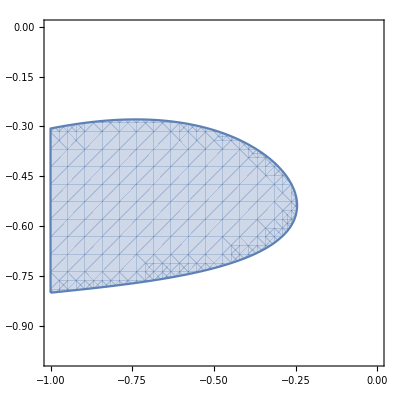

```mathematica
fml3=2.69187+3.7714*a1+6.85916*a2+3.34341*a1^2+1.35293*a1*a2+4.16516*a2^2+0.30672*a1^3+2.81934*a1^2*a2-1.50005*a1*a2^2-2.10735*a2^3;
RegionPlot[fml3≤ 0,{a1,-1,0},{a2,-1,0}]
```

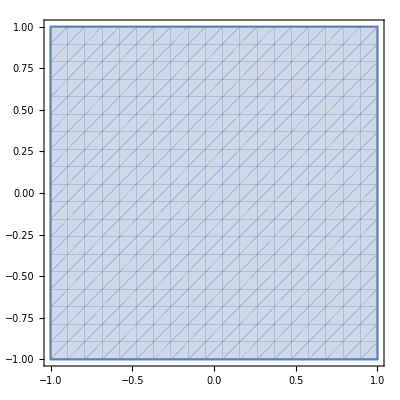

```mathematica
s00=-0.56002-10^(-5)*a2^2;
RegionPlot[s00≤ 0,{a1,-1,1},{a2,-1,1}]
```

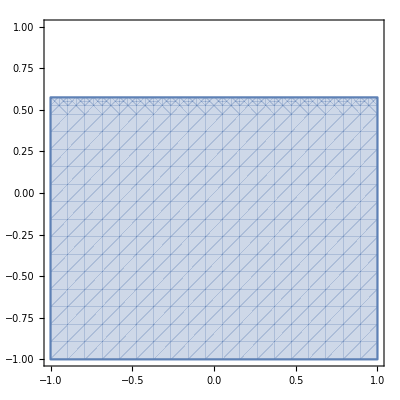

```mathematica
s01=-0.53623+0.26092*a2+0.82853*a2^2+0.59138*a2^3;
RegionPlot[s01≤ 0,{a1,-1,1},{a2,-1,1}]
```

```mathematica
s10=-0.56;
RegionPlot[s10≤ 0,{a1,-1,1},{a2,-1,1}]
```

-Graphics-

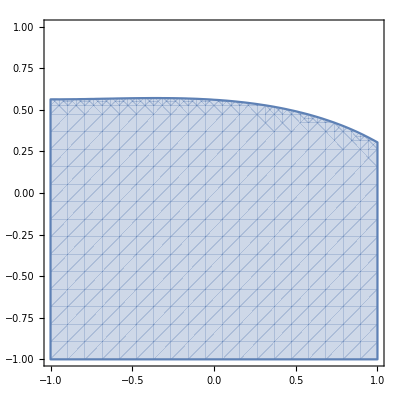

```mathematica
s11=-0.5311+0.00925*a1+0.2889*a2+0.12339*a1^2+0.15832*a1*a2+0.86561*a2^2+0.11022*a1^3+0.17078*a1^2*a2+0.0478*a1*a2^2+0.54927*a2^3;
RegionPlot[s11≤ 0,{a1,-1,1},{a2,-1,1}]
```

{{a1→-1.,a2→-0.5,a3→-1,a4→-1}}

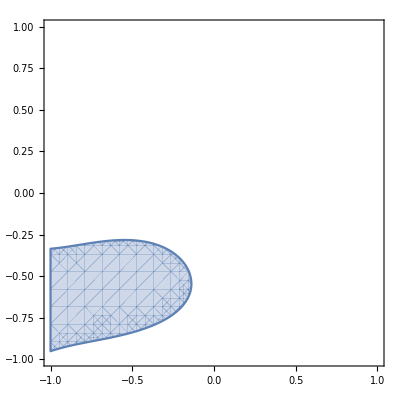

```mathematica
fml4 =2.34708+3.709*a1+6.79674*a2+4.56343*a1^2+0.50408*a1*a2+5.13785*a2^2+0.46131*a1^3+2.46317*a1^2*a2-0.95498*a1*a2^2-1.72283*a2^3-0.91596*a1^4+1.63031*a1^3*a2-1.57411*a1^2*a2^2-0.00418*a1*a2^3-0.74973*a2^4;
FindInstance[{fml4<=0, -1≤ a1≤ 1,-1≤ a2≤ 1,-1≤ a3≤ 1,-1≤ a4≤ 1},{a1,a2,a3,a4}]
RegionPlot[fml4≤ 0, {a1,-1,1},{a2,-1,1}]
```

21

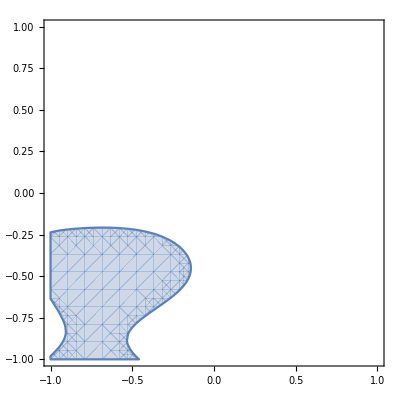

```mathematica
fml5=2.09144+3.49918*a1+7.25218*a2+4.64585*a1^2+1.26871*a1*a2+5.78145*a2^2+1.3642*a1^3+4.75579*a1^2*a2-2.5125*a1*a2^2-4.65644*a2^3-0.92276*a1^4+0.88252*a1^3*a2-1.94575*a1^2*a2^2-0.452*a1*a2^3-1.36834*a2^4-0.30672*a1^5-2.49896*a1^4*a2-1.44654*a1^3*a2^2-0.17869*a1^2*a2^3+2.23803*a1*a2^4+2.57913*a2^5;
Length[MonomialList[fml5]]
RegionPlot[fml5≤ 0, {a1,-1,1},{a2,-1,1}]
```

3

{{a1→0,a2→0,a3→0,a4→0}}

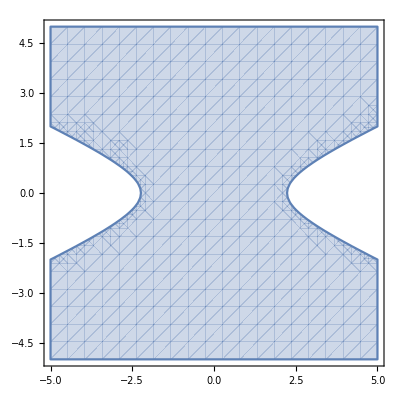

```mathematica
fml6=a1^2-5*a2^2-5;
Length[MonomialList[fml6]]
FindInstance[{fml6<=0, -1≤ a1≤ 1,-1≤ a2≤ 1,-1≤ a3≤ 1,-1≤ a4≤ 1},{a1,a2,a3,a4}]
RegionPlot[fml6≤ 0,{a1,-5,5},{a2,-5,5}]
```

```mathematica
Region
```

```mathematica
Timing[
sol =1.58506-0.28644*a1-9.20816*a2+0.37861*a1^2-0.30923*a1*a2+12.92938*a2^2;
FindInstance[sol≤ 0&&-1≤ a1≤ 1&&-1≤ a2≤ 1&&-1≤ a3≤ 1,{a1,a2,a3}]
]
```

{0.,{{a1→1.,a2→0.443819,a3→-1}}}

```mathematica
inv=x1^2-5*x2^2-5;
invf=(0.95*(x1-0.1*x2^2))^2-5*(0.95*(x2+0.2*x1*x2))^2-5;
```

```mathematica
Reduce[ForAll[{x1,x2},Implies[inv≤ 0&&x1^2≤ 4&&x2^2≤ 4,invf≤ 0]]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Reduce[ForAll[{x1,x2},Implies[x1^2+x2^2≤ 1,inv≤ 0]]]
```

```mathematica
Reduce[ForAll[{x1,x2},Implies[inv≤ 0&&x1^2+x2^2≤ 1,inv≤ 0]]]
```